```mathematica
ClearAll["Global`*"]
Clear["Global`*"]
Needs["PlotLegends`"]
<<"~thomasbuhrmann/Code/Mathematica/Dynamica/Dynamica.m";
```

Dynamica (Version 1.0.5 - 12/6/11), Copyright(c) 1993-2011 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

General::obspkg: "VectorFieldPlots`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

t::shdw: Symbol "t" appears in multiple contexts {"Dynamica`", "Global`"}; definitions in context "Dynamica`" may shadow or be shadowed by other definitions.

```mathematica
meta= DynamicalSystem[
{-A-0.075A^3+0.5A^2F},
{{A,-1,10}},
{{F,0,4}}];
```

```mathematica
(*Manipulate[DisplayPhasePortrait[meta/.F->f],{f,0,10}]*)
(*EquilibriumPoints[meta/.F->1.1]*)
```

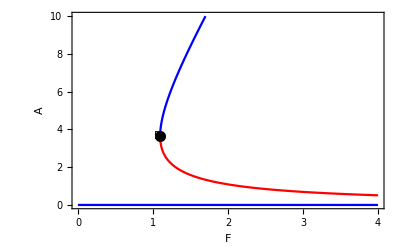

{BifurcationPoint[Fold,{3.65148371670111},{F → 1.09544511501033}]}

```mathematica
DisplayBifurcationDiagram[meta,F]
$BifurcationDiagramBPs
```

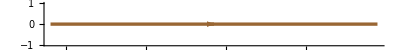

```mathematica
(*DisplayVectorField[meta/.F->2]*)
tr=DisplayTrajectories[meta/.F->2,{{2}},2] (* params: initial condition, time *)

Manipulate[Show[DisplayFlow[meta/.F->f,20.0],DisplayPhasePortrait[meta/.F->f]],{f,0,3}]
```

```mathematica
Manipulate[Show[Plot[-A-0.075A^3+0.5A^2*f,{A,-1,10}],DisplayPhasePortrait[meta/.F->f],DisplayFlow[meta/.F->f,5]],{f,0,4}]
```

```mathematica
kb=0.45;
kf=1;
kd=1;
ODE[F_,kb_,kf_,kd_]:=A'[t]==-(kb/6*A[t]^3)+(kf/2*F*A[t]^2)-kd*A[t];

T=10;
ODEsol[F_,a_]:=NDSolve[{ODE[F,kb,kf,kd],A[0]==a},A[t],{t,0,T}];
ODETrajectory[F_,a_]:=Plot[Evaluate[A[t]/.ODEsol[F,a]],{t,0,T},PlotStyle -> Black,PlotRange->All];
```

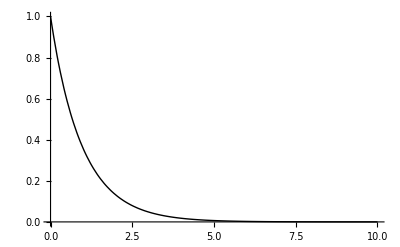

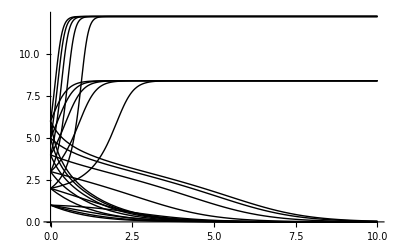

```mathematica
ODETrajectory[0,1]
Show[Table[ODETrajectory[f,a],{f,0.5,2,0.5},{a,1,6,1}],PlotRange->All]
```